```mathematica
m
```

3747.59

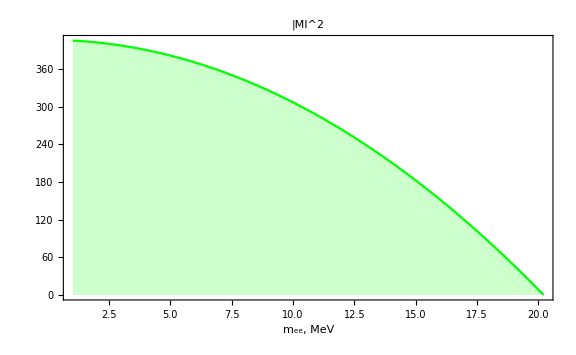

6994.34

4.91158×10^10

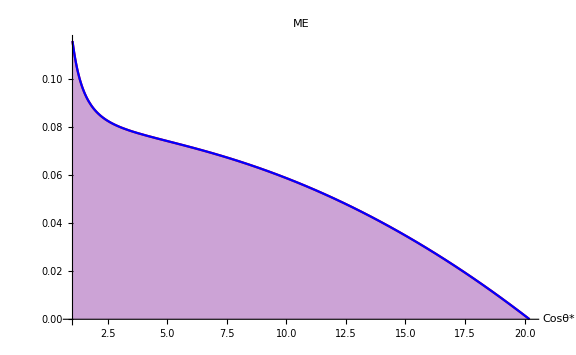

```mathematica
matr[q_,cos_]:=m^2-m3^2-2*m*(e1[q,cos]+e2[q,cos])+4e1[q,cos] e2[q,cos];
matri[q]:=Integrate[matr[q,cc],{cc,-1,1}];
eemin=me;
eemax=m-e3min-me;
cs=0.0;
Plot[{matr[q,cs]},                  {q,qmin,qmax},
PlotLabel->"|MI^2",
Filling->Axis,
PlotRange->{{qmin,qmax},{0,All}},
Frame ->True, FrameLabel->{"m_ee, MeV"," "},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2=NIntegrate[matri[q],{q,qmin,qmax}];
n2
n3=NIntegrate[me2[qq],{qq,qmin,qmax}];
n3
Plot[{matri[q]/n2,me2[q]/n3},                  {q,qmin,qmax},
PlotLabel->"ME",
FrameLabel->{"q","ME"},
Filling->Axis,
PlotRange->{{qmin,qmax},{0,All}},
Axes->True,AxesLabel->{"Cosθ*"," "},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
```

```mathematica
Clear[me]
Clear[m]
Clear[m3]
phs[q]
mxl0dGdm[q,cos]
me
```

(√(-me^2+q^2/4) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(128 m^3 π^3)

((1-cos^2) q √((m^2-(m3-q)^2) (m^2-(m3+q)^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(2048 m^3 π^3)

me

```mathematica
Simplify[((1-cos^2) √(-me^2+q^2/4) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(16 m)]
```

```mathematica
Integrate[((1-cos^2) √(-4 me^2+q^2) ((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(32 m),{cos,-1,1}]
```

(√(-4 me^2+q^2) ((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(24 m)

```mathematica
mxphs[q_]:=(√(-me^2+q^2/4) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(2 m);
mxl0dGdm[q_,cos_]
```

0.0000166774 (1-cos_^2) √(-0.26112+q_^2/4) √((1.40444×10^7-(3727.38-q_)^2) (1.40444×10^7-(3727.38+q_)^2)) (1.97246×10^14+(1.38934×10^7-q_^2)^2-2.80889×10^7 (1.38934×10^7+q_^2))

```mathematica
mee2[q_,cos_]:=Simplify[m^2-m3^2-2 m(e1[q,cos]+e2[q,cos])+4e1[q,cos]e2[q,cos]];
mee2i[q_]:=Integrate[mee2[q,cos],{cos,-1,1}];

(* Formulas   *)
mxme2i[q_]:=((2 me^2+q^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(6 q^2);
mxme2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2)
mxee2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(2 4 m^2 q^2);
mxee2i[q_]:=((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(2 3 m^2 q^2);
mxmel02[q_,cos_]:=1/8 (1-cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2));
mxmel02i[q_]:=1/6 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q);
(*   **********************************  *)

mel0[q_,cc_]:=Simplify[(1/8) (1-cc^2)(m^4+m3^4-2m3^2q^2+q^4-2m^2(m3^2+q^2))];
mel0i[q_]:=Integrate[mel0[q,cc],{cc,-1,1}];
mxee2i[q_]:=((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2);

mxme2[q_,cos_]:=2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2-2*cos^2*(m*pq[q]/(2*q))^2*(q^2-4*me^2);
mxme2i[q_]:=2*(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*(2/3)*(m*pq[q]/(2*q))^2*(q^2-4*me^2);

mqa2[q_,cos_]:=2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2  -  2*cos^2*(m*pq[q]/(2*q))^2*(q^2-4*me^2);
mqa2i[q_]:=Integrate[mqa2[q,cos],{cos,-1,1}];
Simplify[mqa2[q,cos]]
Simplify[mqa2i[q,cos]]
Simplify[mqa2i[q]]
Simplify[mel0[q,cos]]
Simplify[mel0i[q]]
```

((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2)

mqa2i[q,cos]

((2 me^2+q^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(6 q^2)

-1/8 (-1+cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2))

1/6 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q)

```mathematica
mxmel0[q_cos_]:=-1/8 (-1+cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2));
```

```mathematica
mxmel0i[q_,cos_]:=1/6 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q);
```

```mathematica
Simplify[-1/2 m3^2 q^2+1/8 (m^2-m3^2-q^2)^2-1/8 cos^2 (m^2-(m3-q)^2) (m^2-(m3+q)^2)]
mel0[q,cos]
```

-1/8 (-1+cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2))

-1/8 (-1+cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2))

```mathematica
mxme2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2);
```

```mathematica
mxme2i[q_]:=((2 me^2+q^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(6 q^2)
```

```mathematica
mxme2[q_,cos_]:=-1/2 m3^2 q^2+1/8 (m^2-m3^2-q^2)^2-(cos^2 (m^2-(m3-q)^2) (-4 me^2+q^2) (m^2-(m3+q)^2))/(8 q^2);
```

```mathematica
mxme2i[q_]:=((-m^2+(m3-q)^2) (-4 me^2+q^2) (m^2-(m3+q)^2))/(12 q^2)+2 (-1/2 m3^2 q^2+1/8 (m^2-m3^2-q^2)^2)
```

```mathematica
mqa2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2);
mxl0dGdmi[q_]:=(√(-4 me^2+q^2) ((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(24 m);
Integrate[mxl0dGdmi[q],{q,qmin,qmax}]
```

∫_0^(m-m3) (√(-4 me^2+q^2) ((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(24 m)ⅆq

```mathematica
Clear[me];
Clear[m];
Clear[m3];
m=mhe4s;
m3=mhe4;
me=0.51099907;
qmin=0;
qmax=m-m3;

mxl0dGdm[q_,cos_]:=((1-cos^2) q((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(32 m);
mxl0dGdmi[q_]:=(q((m^2-(m3-q)^2) (m^2-(m3+q)^2))^(3/2))/(24 m);
vpk=Integrate[mxl0dGdmi[q],{q,qmin,qmax}]*(2 Pi) (4 Pi)/(2 Pi)^5/16/m^2 ;
Chris=m^5/(4 Pi)^2/(8 Pi) *6.03 10^-13;
Print[" Chris = (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4",Chris]
Print["vpk    = (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4",vpk]
```

Chris = (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4112.31

vpk    = (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4112.355

vpk    = 112.355
Simplify[(4 Pi)^2 α^2 G^2/Λ^4]

```mathematica
Simplify[(4 Pi)^2 α^2 G^2/Λ^4]
3.131303219591601*^12*(4 Pi)^2*8*Pi/m^5*4*Pi/(2 Pi)^5 /16/m^2
```

(16 G^2 π^2 α^2)/Λ^4

9.60087×10^-14

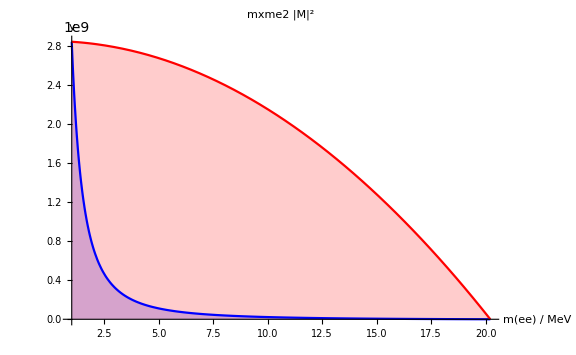

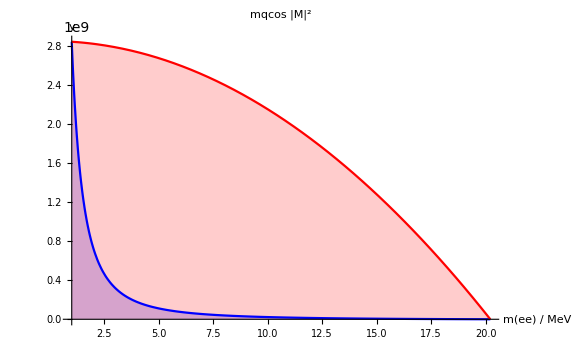

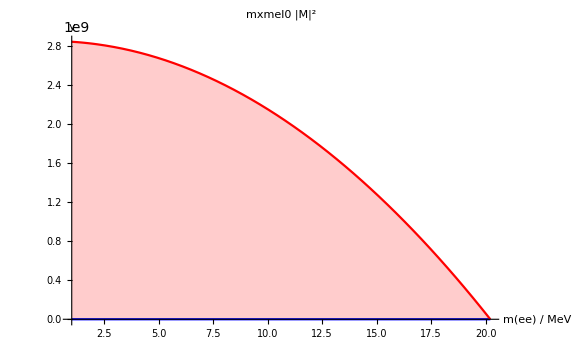

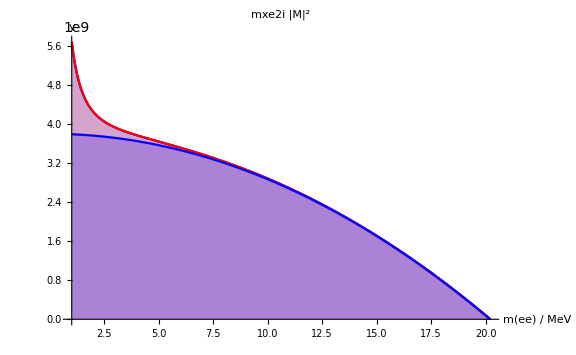

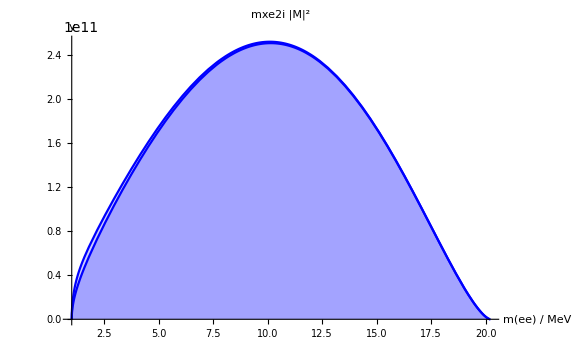

```mathematica
m=mhe4s;
m3=mhe4;
me=0.51099907;
cs1=1.;
cs2=0.;
Plot[{mxme2[q,cs1],mxme2[q,cs2]},                   {q,qmin,qmax},
PlotLabel->"mxme2 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{mqcos[q,cs1],mqcos[q,cs2]},                   {q,qmin,qmax},
PlotLabel->"mqcos |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{mxmel0[q,cs1],mxmel0[q,cs2]},                   {q,qmin,qmax},
PlotLabel->"mxmel0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{mxme2i[q],mqcosi[q],mel0i[q]} ,                  {q,qmin,qmax},
PlotLabel->"mxe2i |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{mxme2i[q]*phs[q],mqcosi[q]*pha[q],mxl0dGdmi[q]} ,                  {q,qmin,qmax},
PlotLabel->"mxe2i |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
```

```mathematica
mxme2[q_,cos_]:=((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2);
mxme2i[q_]:=Integrate[mxme2[q,cc],{cc,-1,1}];
mxme2i[q]
```

```mathematica
mxme2i[q_]:=(2 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2);
```

```mathematica
mxel0i[q_]:=1/6 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q);
```

((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2)

```mathematica
mxmel0[q_,cos_]:=1/8 (1-cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2));
```

((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2)

```mathematica
mxee2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(4 m^2 q^2);
```

```mathematica
mxee2i[q_]:=((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2);
```

```mathematica
matrix[q_]:=Integrate[((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(4 m^2 q^2),{cos,-1,1}]
matrix2[q_]:=Simplify[matrix[q]]
matrix2[q]
```

((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(3 m^2 q^2)

```mathematica
Simplify[me2[q]]
```

```mathematica
mee2[q_]:=((2 me^2+q^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(6 q^2)
```

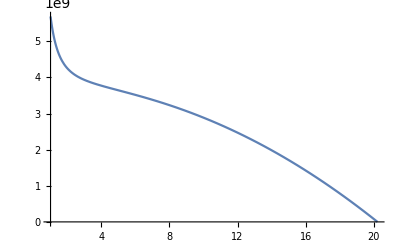

-Graphics-

```mathematica
Plot[{me2[q]},{q,qmin,qmax}]
```